```mathematica
Series[x^ϵ-1, {ϵ, 0, 2}]
```

Log[x] ϵ+1/2 Log[x]^2 ϵ^2+O[ϵ]^3

```mathematica
Φ0[x_, p_, q_ ] :=x Log[p] + (1-x)Log[q]  -x Log[x] - (1-x)Log[1-x];
G[x_, z1_,z2_,X0_,λ_, ϵ_] := (λ/ϵ)(x (z1^ϵ-1) 
+(1-x) (z2^ϵ-1)) + X0^ϵ;
g[x_, z1_,z2_,X0_,λ_, ϵ_] = Normal[Series[G[x, z1,z2,X0,λ, ϵ], {ϵ, 0, 1}]];
Φ1[x_, z1_, z2_, X0_, ϵ_, λ_ ] := (1/λ)Log[G[x, z1,z2,X0,λ, ϵ]];
ϕ1[x_, z1_, z2_, X0_, ϵ_, λ_ ] := (1/λ)Log[g[x, z1,z2,X0,λ, ϵ]];
```

```mathematica
Φ = Φ0[x, p, q ] + ϕ1[x, z1, z2, X0, ϵ, λ ]
```

x Log[p]+(1-x) Log[q]-(1-x) Log[1-x]-x Log[x]+Log[1+λ (x Log[z1]-(-1+x) Log[z2])+ϵ (Log[X0]+λ (1/2 x Log[z1]^2-1/2 (-1+x) Log[z2]^2))]/λ

```mathematica
Solve[D[Φ /. ϵ->0 , x]== 0, x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Log[p]-Log[q]+Log[1-x]-Log[x]+(Log[z1]-Log[z2])/(1+λ (x Log[z1]-(-1+x) Log[z2]))==0,x]

```mathematica
Root[D[(Φ /. ϵ->0 /. q->p) // FullSimplify, x]  // FullSimplify, x]
```

```mathematica
a  = D[(),x] // FullSimplify
```

2 (1/(1-λ+2 x λ)+ArcTanh[1-2 x])

```mathematica
Solve[a ==0, x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[1/x+2 ArcTanh[1-2 x]==0,x]

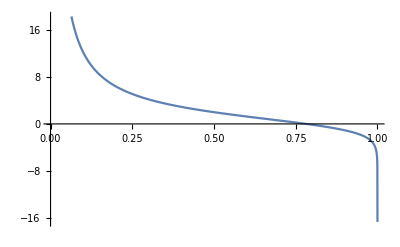

```mathematica
Plot[a, {x, 0, 1}]
```

```mathematica
b = a /. x-> 1/2(y +1)
```

2/(1+y)-2 ArcTanh[y]

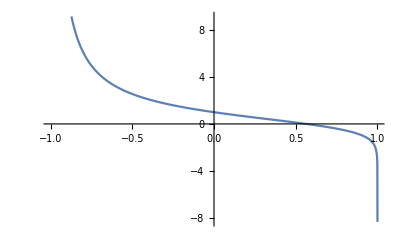

```mathematica
Plot[{-ArcTanh[y]+ 1/(1+y)}, {y, -1, 1}]
```

```mathematica
FindRoot[b, {y, 0.5}]
```

{y→0.564377}

```mathematica
FullSimplify[Φ /. ϵ->0 /. {q->1-p, z1-> ⅇ, z2-> 1/ⅇ} /. p-> 1/ⅇ]
```

-1+Log[-1+ⅇ]+(-1+x) Log[1-x]-x Log[(-1+ⅇ) x]+Log[1-λ+2 x λ]/λ

```mathematica
D[Φ, x] /. ϵ->0 // FullSimplify
```

2 ArcTanh[1-2 x]+Log[p]-Log[q]+(Log[z1]-Log[z2])/(1+x λ Log[z1]+(λ-x λ) Log[z2])

```mathematica
Φ2 = Φ0[x, p, q ] + Φ1[x, z1, z2, X0, ϵ, λ ]
```

x Log[p]+(1-x) Log[q]-(1-x) Log[1-x]-x Log[x]+Log[X0^ϵ+((x (-1+z1^ϵ)+(1-x) (-1+z2^ϵ)) λ)/ϵ]/λ

```mathematica
D[Φ2, x]
```

(z1^ϵ-z2^ϵ)/(ϵ (X0^ϵ+((x (-1+z1^ϵ)+(1-x) (-1+z2^ϵ)) λ)/ϵ))+Log[p]-Log[q]+Log[1-x]-Log[x]

```mathematica
A = D[Φ2, x] // FullSimplify
```

(z1^ϵ-z2^ϵ)/(X0^ϵ ϵ+(-1+z2^ϵ+x (z1^ϵ-z2^ϵ)) λ)+2 ArcTanh[1-2 x]+Log[p]-Log[q]

```mathematica
B = X0^ϵ ϵ +(-1+z2^ϵ+x (z1^ϵ-z2^ϵ)) λ
```

X0^ϵ ϵ+(-1+z2^ϵ+x (z1^ϵ-z2^ϵ)) λ

```mathematica
Normal[Series[A, {ϵ, 0, 1}]]
```

2 ArcTanh[1-2 x]+Log[p]-Log[q]+(ϵ (-2 Log[X0] Log[z1]+Log[z1]^2+2 Log[X0] Log[z2]+λ Log[z1]^2 Log[z2]-Log[z2]^2-λ Log[z1] Log[z2]^2))/(2 (1+x λ Log[z1]+λ Log[z2]-x λ Log[z2])^2)+(Log[z1]-Log[z2])/(1+λ (x (Log[z1]-Log[z2])+Log[z2]))

```mathematica
Normal[Series[B, {ϵ, 0, 1}]]
```

ϵ (1+λ (x (Log[z1]-Log[z2])+Log[z2]))

```mathematica
A2 = D[Φ2, {x,2}] // FullSimplify
```

1/(-1+x)-1/x-((z1^ϵ-z2^ϵ)^2 λ)/((X0^ϵ ϵ+(-1+x z1^ϵ+z2^ϵ-x z2^ϵ) λ)^2)

```mathematica
Solve[(Limit[A , λ->∞] // FullSimplify) ==0, x, Assumptions->{p>0, p <1,  q>0 , q<1, p+q ==1 }]
```

Solve::useq: The answer found by Solve contains equational condition(s) {0==2 ArcTanh[1-2 p]+Log[-p/(-1+p)]}. A likely reason for this is that the solution set depends on branch cuts of Wolfram Language functions.

{{x→ConditionalExpression[p, 2 ArcTanh[1-2 p]+Log[-p/(-1+p)]==0]}}

```mathematica
(Limit[A , λ->0] // FullSimplify)
```

(X0^-ϵ (z1^ϵ-z2^ϵ))/ϵ+2 ArcTanh[1-2 x]+Log[p]-Log[q]

```mathematica
x /. Solve[2 ArcTanh[1- 2 x] + c == 0, x, Assumptions->{c>0}][[1]] /. c-> ((X0^-ϵ (z1^ϵ-z2^ϵ))/ϵ +Log[p]-Log[q])
```

1/2+1/2 Tanh[1/2 ((X0^-ϵ (z1^ϵ-z2^ϵ))/ϵ+Log[p]-Log[q])]

```mathematica
Limit[%, ϵ->0]
```

1/2 (1+Tanh[1/2 (Log[p]-Log[q]+Log[z1]-Log[z2])])

```mathematica
TrigToExp[1/2 (1-Tanh[-x/2])] // Simplify
```

ⅇ^x/(1+ⅇ^x)

```mathematica
Z1 = Exp[(z1^ζ-1)/(ζ X0^ζ)];
Z2 = Exp[(z2^ζ-1)/(ζ X0^ζ)];
A = (p Z1 Log[Z1] + q Z2 Log[Z2])/(p Z1 + q Z2);
B = (1 + T ζ A)^(1/ζ);
ans = X0 (p Z1 + q Z2)^T B Exp[-T A]
```